```mathematica
DSolve[f'[R]==R^2/(f[R]^2), f[R], R]
```

{{f[R]→(R^3+3 C[1])^(1/3)},{f[R]→-(-1)^(1/3) (R^3+3 C[1])^(1/3)},{f[R]→(-1)^(2/3) (R^3+3 C[1])^(1/3)}}

```mathematica
w[l1_, l2_,l3_, a_,b_]:=a (l1^2+l2^2+l3^2-3)+b (l1^(-2)+ l2^(-2)+l3^(-2)-3);
hatw[l_, a_, b_]:=(1/l^2)D[w[x^(-2),x,x, a,b],x]/.x->l;
```

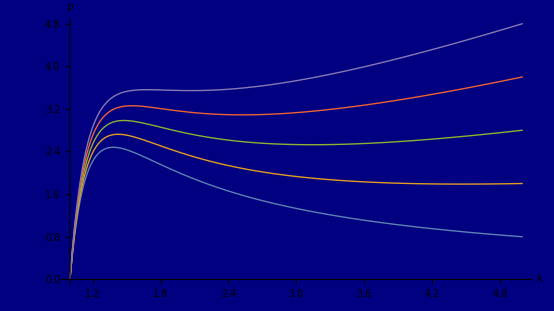

```mathematica
Plot[{hatw[l,1,0],hatw[l,1,0.05],hatw[l,1,0.1], hatw[l,1,0.15], hatw[l, 1, 0.2]},{l, 1, 5},AspectRatio->9/16,Background->RGBColor[0,0,0.5], AxesStyle->{Directive[Thick,RGBColor[1,0.97,0]], Directive[Thick,RGBColor[1,0.97,0]]}, TicksStyle->RGBColor[1,0.97,0], PlotStyle->Thick, AxesLabel->{Style["λ",Italic, 24], Style["", Italic,24]}]
```

```mathematica
hatw[1, 1,2]
```

General::ivar: 1 is not a valid variable.

∂_1 0

```mathematica
D[w[l^(-2),l,l, a,b],l]
```

a (-4/l^5+4 l)+b (-4/l^3+4 l^3)

```mathematica
ClearAll[l]
```